```mathematica
datFileLocalChernlocation="/data/topo_super/local_chern/";
datfileOBCName0="H11_t0=1.0_t=1.0_m_0=0.0_mu=1.2_Delta=0.5_x_periodic=0_y_periodic=0_L=60_m=0.6180339887498949_c1=4_c2=10";
```

```mathematica
datfileOBCName1="H11_t0=1.0_t=1.0_m_0=1.0_mu=1.2_Delta=0.5_x_periodic=0_y_periodic=0_L=60_m=0.6180339887498949_c1=4_c2=10";

datfileOBCName2="H11_t0=1.0_t=1.0_m_0=2.0_mu=0.0_Delta=0.5_x_periodic=0_y_periodic=0_L=60_m=0.6180339887498949_c1=4_c2=10";

(** datfileOBCName3="H11_t0=1.0_t=1.0_m_0=3.0_mu=0.0_Delta=0.5_x_periodic=0_y_periodic=0_L=60_m=0.6180339887498949_c1=4_c2=10"; **)
```

```mathematica
list0=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLocalChernlocation,datfileOBCName0,".csv"]]];
```

```mathematica
Dimensions[listMinus1]
```

{60}

```mathematica
list1=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLocalChernlocation,datfileOBCName1,".csv"]]];
```

```mathematica
list2=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLocalChernlocation,datfileOBCName2,".csv"]]];
```

```mathematica
(** list3=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLocalChernlocation,datfileOBCName3,".csv"]]]; **)
```

```mathematica
listMinus2=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLocalChernlocation,"H11_t0=1.0_t=1.0_m_0=-2.0_mu=0.0_Delta=0.5_x_periodic=0_y_periodic=0_L=60_m=0.6180339887498949_c1=4_c2=10.csv"]]];
```

```mathematica
listMinus1=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLocalChernlocation,"H11_t0=1.0_t=1.0_m_0=-1.0_mu=1.2_Delta=0.5_x_periodic=0_y_periodic=0_L=60_m=0.6180339887498949_c1=4_c2=10.csv"]]];
```

```mathematica
Lx=Dimensions[list1][[1]]
```

60

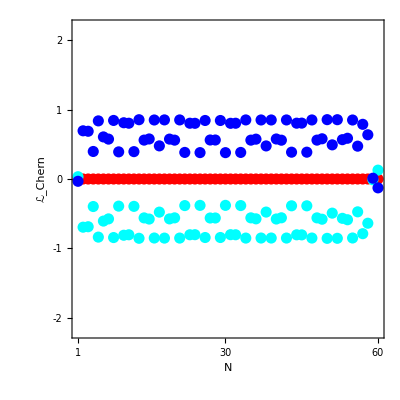

```mathematica
Show[ListPlot[list0,PlotRange->{{1,Lx},{-2.2,2.2}},Frame->True,PlotStyle-> {Red,PointSize[0.02]},Axes->False],
ListPlot[list1,PlotRange->{-2.2,2.2},Frame->True,PlotStyle-> {Cyan,PointSize[0.02]},Axes->False],
(** ListPlot[list2,PlotRange->{-2.2,2.2},Frame->True,PlotStyle-> {Blue,PointSize[0.02]},Axes->False],**)
(** ListPlot[list3,PlotRange->{-2.2,2.2},Frame->True,PlotStyle-> {Black,PointSize[0.01]},Axes->False], **)
ListPlot[listMinus1,PlotRange->{-2.2,2.2},Frame->True,PlotStyle-> {Blue,PointSize[0.02]},Axes->False],
(**ListPlot[listMinus2,PlotRange->{-2.2,2.2},Frame->True,PlotStyle-> {Cyan,PointSize[0.02]},Axes->False],**)
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 24,
FrameTicks->{ {{{-2,"-2"},{-1,"-1"},{0,"0"},{1,"1"},{2,"2"}},None},{{1,Lx/2,Lx},None}},
ImageSize-> 400,AspectRatio-> 1,
FrameLabel->{"N","ℒ_Chern"},RotateLabel->False]
```